```mathematica
V0=1;Δ=1;
```

```mathematica
v1[x_]:=(Sign[x]+1)/2.0 - (Sign[x-3*π/Δ]+1) +(Sign[x-4*π/Δ]+1)/2.0
```

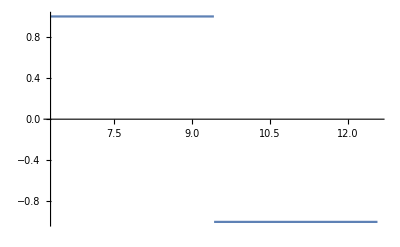

```mathematica
Plot[v1[x],{x,2*π,4*π}]
```

```mathematica
v2[x_]:=(((Sign[x]+1)/2.0) -((Sign[x-4.0*π/Δ]+1)/2.0))*Sin[Δ*x]
```

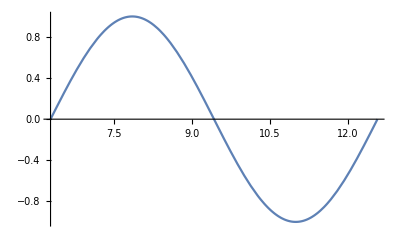

```mathematica
Plot[v2[x],{x,2*π,4*π}]
```

```mathematica
v3[x_]:=(((Sign[x]+1)/2.0) -((Sign[x-3*π/Δ]+1)/2.0))*((x-2*π)/π)+(((Sign[x-3*π/Δ]+1)/2.0)-((Sign[x-4*π/Δ]+1.0)/2.0))*((4*π-x)/π)
```

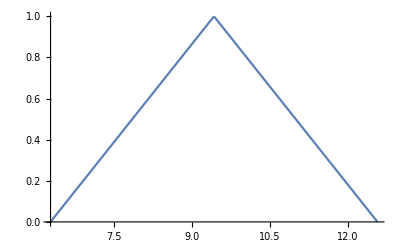

```mathematica
Plot[v3[x],{x,2*π,4*π}]
```

```mathematica
Block[{x},Do[f1[i][x_]=(Sign[x]+1)/2.0 - (Sign[x-(2*i-1)*π/Δ]+1) +(Sign[x-(2*i)*π/Δ]+1)/2.0,{i,1,10}]]
```

```mathematica
Definition @ f1
```

f1[1][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-2 π+x])-Sign[-π+x]
 
f1[2][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-4 π+x])-Sign[-3 π+x]
 
f1[3][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-6 π+x])-Sign[-5 π+x]
 
f1[4][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-8 π+x])-Sign[-7 π+x]
 
f1[5][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-10 π+x])-Sign[-9 π+x]
 
f1[6][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-12 π+x])-Sign[-11 π+x]
 
f1[7][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-14 π+x])-Sign[-13 π+x]
 
f1[8][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-16 π+x])-Sign[-15 π+x]
 
f1[9][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-18 π+x])-Sign[-17 π+x]
 
f1[10][x_]=-1+0.5 (1+Sign[x])+0.5 (1+Sign[-20 π+x])-Sign[-19 π+x]

```mathematica
Block[{t},g1[t_]=Piecewise[Table[{f1[i][t],(i-1)*π<t<i*2*π},{i,10}]]];
```

```mathematica
Definition @ g1
```

g1[t_]=Piecewise[{{-1+0.5 (1+Sign[t])+0.5 (1+Sign[-2 π+t])-Sign[-π+t], 0<t<2 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-4 π+t])-Sign[-3 π+t], π<t<4 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-6 π+t])-Sign[-5 π+t], 2 π<t<6 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-8 π+t])-Sign[-7 π+t], 3 π<t<8 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-10 π+t])-Sign[-9 π+t], 4 π<t<10 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-12 π+t])-Sign[-11 π+t], 5 π<t<12 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-14 π+t])-Sign[-13 π+t], 6 π<t<14 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-16 π+t])-Sign[-15 π+t], 7 π<t<16 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-18 π+t])-Sign[-17 π+t], 8 π<t<18 π}, {-1+0.5 (1+Sign[t])+0.5 (1+Sign[-20 π+t])-Sign[-19 π+t], 9 π<t<20 π}, {0, True}}]

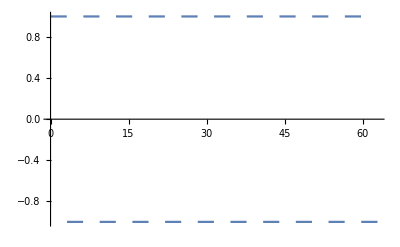

```mathematica
Plot[g1[t],{t,0,20*π}]
```

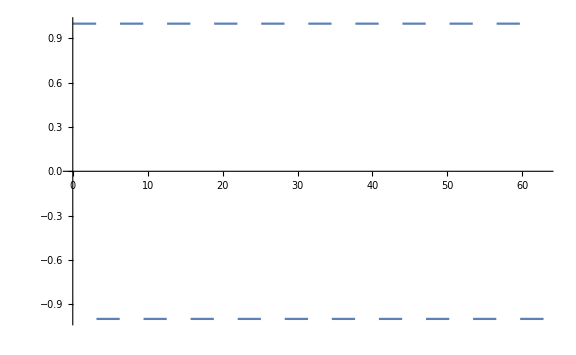

```mathematica
Show[%11,ImageSize->Large]
```

```mathematica
Block[{x},Do[f2[i][x_]=(((Sign[x]+1)/2.0) -((Sign[x-(2*i)*π/Δ]+1)/2.0))*Sin[Δ*x]
,{i,1,10}]]
```

```mathematica
Block[{t},g2[t_]=Piecewise[Table[{f2[i][t],(i-1)*π<t<i*2*π},{i,10}]]];
```

```mathematica
Definition @ g2
```

g2[t_]=Piecewise[{{(0.5 (1+Sign[t])-0.5 (1+Sign[-2 π+t])) Sin[t], 0<t<2 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-4 π+t])) Sin[t], π<t<4 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-6 π+t])) Sin[t], 2 π<t<6 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-8 π+t])) Sin[t], 3 π<t<8 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-10 π+t])) Sin[t], 4 π<t<10 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-12 π+t])) Sin[t], 5 π<t<12 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-14 π+t])) Sin[t], 6 π<t<14 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-16 π+t])) Sin[t], 7 π<t<16 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-18 π+t])) Sin[t], 8 π<t<18 π}, {(0.5 (1+Sign[t])-0.5 (1+Sign[-20 π+t])) Sin[t], 9 π<t<20 π}, {0, True}}]

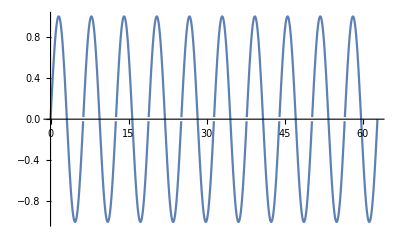

```mathematica
Plot[g2[t],{t,0,20*π}]
```

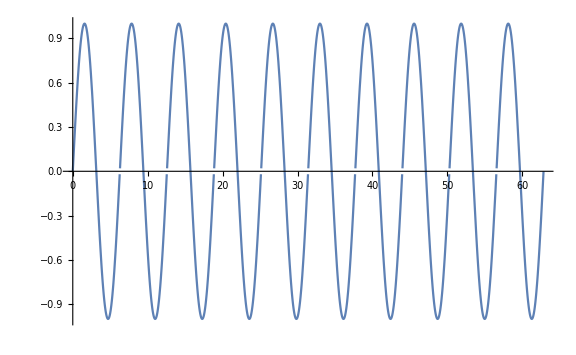

```mathematica
Show[%21,ImageSize->Large]
```

```mathematica
Block[{x},Do[f3[i][x_]=(((Sign[x]+1)/2.0) -((Sign[x-(2*i-1)*π/Δ]+1)/2.0))*(((x-2*i*π)/π)+2)+(((Sign[x-(2*i-1)*π/Δ]+1)/2.0)-((Sign[x-2*i*π/Δ]+1.0)/2.0))*((2*i*π-x)/π)
,{i,1,10}]]
```

```mathematica
Block[{t},g3[t_]=Piecewise[Table[{f3[i][t],(i-1)*π<t<2*π*i},{i,10}]]];
```

```mathematica
Definition @ g3
```

g3[t_]=Piecewise[{{(2+(-2 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-π+t]))+((2 π-t) (-0.5 (1.+Sign[-2 π+t])+0.5 (1+Sign[-π+t])))/π, 0<t<2 π}, {(2+(-4 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-3 π+t]))+((4 π-t) (-0.5 (1.+Sign[-4 π+t])+0.5 (1+Sign[-3 π+t])))/π, π<t<4 π}, {(2+(-6 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-5 π+t]))+((6 π-t) (-0.5 (1.+Sign[-6 π+t])+0.5 (1+Sign[-5 π+t])))/π, 2 π<t<6 π}, {(2+(-8 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-7 π+t]))+((8 π-t) (-0.5 (1.+Sign[-8 π+t])+0.5 (1+Sign[-7 π+t])))/π, 3 π<t<8 π}, {(2+(-10 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-9 π+t]))+((10 π-t) (-0.5 (1.+Sign[-10 π+t])+0.5 (1+Sign[-9 π+t])))/π, 4 π<t<10 π}, {(2+(-12 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-11 π+t]))+((12 π-t) (-0.5 (1.+Sign[-12 π+t])+0.5 (1+Sign[-11 π+t])))/π, 5 π<t<12 π}, {(2+(-14 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-13 π+t]))+((14 π-t) (-0.5 (1.+Sign[-14 π+t])+0.5 (1+Sign[-13 π+t])))/π, 6 π<t<14 π}, {(2+(-16 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-15 π+t]))+((16 π-t) (-0.5 (1.+Sign[-16 π+t])+0.5 (1+Sign[-15 π+t])))/π, 7 π<t<16 π}, {(2+(-18 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-17 π+t]))+((18 π-t) (-0.5 (1.+Sign[-18 π+t])+0.5 (1+Sign[-17 π+t])))/π, 8 π<t<18 π}, {(2+(-20 π+t)/π) (0.5 (1+Sign[t])-0.5 (1+Sign[-19 π+t]))+((20 π-t) (-0.5 (1.+Sign[-20 π+t])+0.5 (1+Sign[-19 π+t])))/π, 9 π<t<20 π}, {0, True}}]

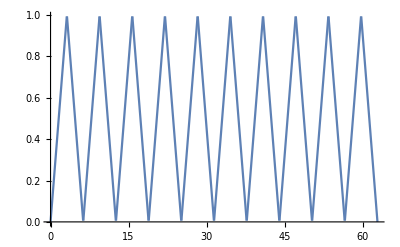

```mathematica
Plot[g3[t],{t,0,20*π}]
```

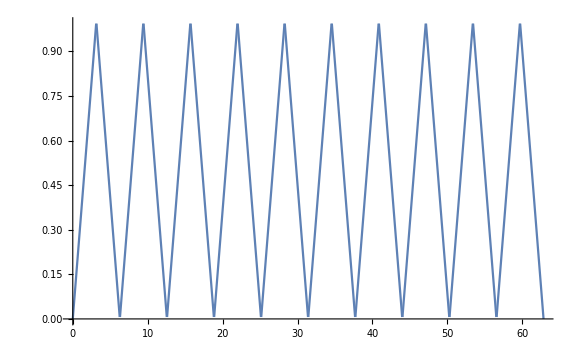

```mathematica
Show[%26,ImageSize->Large]
```

```mathematica
d1[k_]:=Integrate[g1[t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
d11[k_]=d1[k]*Conjugate[d1[k]]
```

Conjugate[Piecewise[{{0.+40. ⅈ, k>62.8319}, {(0.+1. ⅈ) (3.+ⅇ^((0.+1. ⅈ) k)), 3.14159<k≤6.28319}, {(0.+1. ⅈ) (7.+ⅇ^((0.+1. ⅈ) k)), 9.42478<k≤12.5664}, {(0.+1. ⅈ) (11.+ⅇ^((0.+1. ⅈ) k)), 15.708<k≤18.8496}, {(0.+1. ⅈ) (15.+ⅇ^((0.+1. ⅈ) k)), 21.9911<k≤25.1327}, {(0.+1. ⅈ) (19.+ⅇ^((0.+1. ⅈ) k)), 28.2743<k≤31.4159}, {(0.+1. ⅈ) (23.+ⅇ^((0.+1. ⅈ) k)), 34.5575<k≤37.6991}, {(0.+1. ⅈ) (27.+ⅇ^((0.+1. ⅈ) k)), 40.8407<k≤43.9823}, {(0.+1. ⅈ) (31.+ⅇ^((0.+1. ⅈ) k)), 47.1239<k≤50.2655}, {(0.+1. ⅈ) (35.+ⅇ^((0.+1. ⅈ) k)), 53.4071<k≤56.5487}, {(0.+1. ⅈ) (39.+ⅇ^((0.+1. ⅈ) k)), 59.6903<k≤62.8319}, {(0.-1. ⅈ) (-37.+Cos[k]+(0.+1. ⅈ) Sin[k]), 56.5487<k≤59.6903}, {(0.-1. ⅈ) (-33.+Cos[k]+(0.+1. ⅈ) Sin[k]), 50.2655<k≤53.4071}, {(0.-1. ⅈ) (-29.+Cos[k]+(0.+1. ⅈ) Sin[k]), 43.9823<k≤47.1239}, {(0.-1. ⅈ) (-25.+Cos[k]+(0.+1. ⅈ) Sin[k]), 37.6991<k≤40.8407}, {(0.-1. ⅈ) (-21.+Cos[k]+(0.+1. ⅈ) Sin[k]), 31.4159<k≤34.5575}, {(0.-1. ⅈ) (-17.+Cos[k]+(0.+1. ⅈ) Sin[k]), 25.1327<k≤28.2743}, {(0.-1. ⅈ) (-13.+Cos[k]+(0.+1. ⅈ) Sin[k]), 18.8496<k≤21.9911}, {(0.-1. ⅈ) (-9.+Cos[k]+(0.+1. ⅈ) Sin[k]), 12.5664<k≤15.708}, {(0.-1. ⅈ) (-5.+Cos[k]+(0.+1. ⅈ) Sin[k]), 6.28319<k≤9.42478}, {(0.-1. ⅈ) (-1.+Cos[k]+(0.+1. ⅈ) Sin[k]), True}}]] (Piecewise[{{0.+40. ⅈ, k>62.8319}, {(0.+1. ⅈ) (3.+ⅇ^((0.+1. ⅈ) k)), 3.14159<k≤6.28319}, {(0.+1. ⅈ) (7.+ⅇ^((0.+1. ⅈ) k)), 9.42478<k≤12.5664}, {(0.+1. ⅈ) (11.+ⅇ^((0.+1. ⅈ) k)), 15.708<k≤18.8496}, {(0.+1. ⅈ) (15.+ⅇ^((0.+1. ⅈ) k)), 21.9911<k≤25.1327}, {(0.+1. ⅈ) (19.+ⅇ^((0.+1. ⅈ) k)), 28.2743<k≤31.4159}, {(0.+1. ⅈ) (23.+ⅇ^((0.+1. ⅈ) k)), 34.5575<k≤37.6991}, {(0.+1. ⅈ) (27.+ⅇ^((0.+1. ⅈ) k)), 40.8407<k≤43.9823}, {(0.+1. ⅈ) (31.+ⅇ^((0.+1. ⅈ) k)), 47.1239<k≤50.2655}, {(0.+1. ⅈ) (35.+ⅇ^((0.+1. ⅈ) k)), 53.4071<k≤56.5487}, {(0.+1. ⅈ) (39.+ⅇ^((0.+1. ⅈ) k)), 59.6903<k≤62.8319}, {(0.-1. ⅈ) (-37.+Cos[k]+(0.+1. ⅈ) Sin[k]), 56.5487<k≤59.6903}, {(0.-1. ⅈ) (-33.+Cos[k]+(0.+1. ⅈ) Sin[k]), 50.2655<k≤53.4071}, {(0.-1. ⅈ) (-29.+Cos[k]+(0.+1. ⅈ) Sin[k]), 43.9823<k≤47.1239}, {(0.-1. ⅈ) (-25.+Cos[k]+(0.+1. ⅈ) Sin[k]), 37.6991<k≤40.8407}, {(0.-1. ⅈ) (-21.+Cos[k]+(0.+1. ⅈ) Sin[k]), 31.4159<k≤34.5575}, {(0.-1. ⅈ) (-17.+Cos[k]+(0.+1. ⅈ) Sin[k]), 25.1327<k≤28.2743}, {(0.-1. ⅈ) (-13.+Cos[k]+(0.+1. ⅈ) Sin[k]), 18.8496<k≤21.9911}, {(0.-1. ⅈ) (-9.+Cos[k]+(0.+1. ⅈ) Sin[k]), 12.5664<k≤15.708}, {(0.-1. ⅈ) (-5.+Cos[k]+(0.+1. ⅈ) Sin[k]), 6.28319<k≤9.42478}, {(0.-1. ⅈ) (-1.+Cos[k]+(0.+1. ⅈ) Sin[k]), True}}])

```mathematica
Plot[d11[k],{k,0,20*π}]
```

$Aborted

```mathematica
d2[k_]:=Integrate[g2[t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
d22[k_]=d2[k]*Conjugate[d2[k]]
```

Conjugate[Piecewise[{{0.25 (1.-1. ⅇ^((0.+2. ⅈ) k)+(0.+2. ⅈ) k), k≤62.8319}, {0.+31.4159 ⅈ, True}}]] (Piecewise[{{0.25 (1.-1. ⅇ^((0.+2. ⅈ) k)+(0.+2. ⅈ) k), k≤62.8319}, {0.+31.4159 ⅈ, True}}])

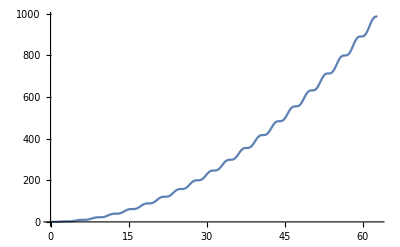

```mathematica
Plot[d22[k],{k,0,20*π}]
```

```mathematica
d3[k_]:=Integrate[g3[t]*Exp[ⅈ*Δ*t],{t,0,k},Assumptions->{t>0,k>0}]
```

```mathematica
d33[k_]=d3[k]*Conjugate[d3[k]]
```

Conjugate[Piecewise[{{-12.7324, k>62.8319}, {0.31831 (-5.+(1.+6.28319 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 6.28319<k≤9.42478}, {0.31831 (-9.+(1.+12.5664 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 12.5664<k≤15.708}, {0.31831 (-13.+(1.+18.8496 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 18.8496<k≤21.9911}, {0.31831 (-17.+(1.+25.1327 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 25.1327<k≤28.2743}, {0.31831 (-21.+(1.+31.4159 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 31.4159<k≤34.5575}, {0.31831 (-25.+(1.+37.6991 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 37.6991<k≤40.8407}, {0.31831 (-29.+(1.+43.9823 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 43.9823<k≤47.1239}, {0.31831 (-33.+(1.+50.2655 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 50.2655<k≤53.4071}, {0.31831 (-37.+(1.+56.5487 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 56.5487<k≤59.6903}, {(0.-0.31831 ⅈ) ((0.-3. ⅈ)+(6.28319-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 3.14159<k≤6.28319}, {(0.-0.31831 ⅈ) ((0.-7. ⅈ)+(12.5664-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 9.42478<k≤12.5664}, {(0.-0.31831 ⅈ) ((0.-11. ⅈ)+(18.8496-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 15.708<k≤18.8496}, {(0.-0.31831 ⅈ) ((0.-15. ⅈ)+(25.1327-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 21.9911<k≤25.1327}, {(0.-0.31831 ⅈ) ((0.-19. ⅈ)+(31.4159-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 28.2743<k≤31.4159}, {(0.-0.31831 ⅈ) ((0.-23. ⅈ)+(37.6991-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 34.5575<k≤37.6991}, {(0.-0.31831 ⅈ) ((0.-27. ⅈ)+(43.9823-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 40.8407<k≤43.9823}, {(0.-0.31831 ⅈ) ((0.-31. ⅈ)+(50.2655-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 47.1239<k≤50.2655}, {(0.-0.31831 ⅈ) ((0.-35. ⅈ)+(56.5487-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 53.4071<k≤56.5487}, {(0.-0.31831 ⅈ) ((0.-39. ⅈ)+(62.8319-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 59.6903<k≤62.8319}, {0.31831 (-1.+Cos[k]-(0.+1. ⅈ) k Cos[k]+(0.+1. ⅈ) Sin[k]+k Sin[k]), True}}]] (Piecewise[{{-12.7324, k>62.8319}, {0.31831 (-5.+(1.+6.28319 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 6.28319<k≤9.42478}, {0.31831 (-9.+(1.+12.5664 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 12.5664<k≤15.708}, {0.31831 (-13.+(1.+18.8496 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 18.8496<k≤21.9911}, {0.31831 (-17.+(1.+25.1327 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 25.1327<k≤28.2743}, {0.31831 (-21.+(1.+31.4159 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 31.4159<k≤34.5575}, {0.31831 (-25.+(1.+37.6991 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 37.6991<k≤40.8407}, {0.31831 (-29.+(1.+43.9823 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 43.9823<k≤47.1239}, {0.31831 (-33.+(1.+50.2655 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 50.2655<k≤53.4071}, {0.31831 (-37.+(1.+56.5487 ⅈ) ⅇ^((0.+1. ⅈ) k)-(0.+1. ⅈ) ⅇ^((0.+1. ⅈ) k) k), 56.5487<k≤59.6903}, {(0.-0.31831 ⅈ) ((0.-3. ⅈ)+(6.28319-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 3.14159<k≤6.28319}, {(0.-0.31831 ⅈ) ((0.-7. ⅈ)+(12.5664-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 9.42478<k≤12.5664}, {(0.-0.31831 ⅈ) ((0.-11. ⅈ)+(18.8496-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 15.708<k≤18.8496}, {(0.-0.31831 ⅈ) ((0.-15. ⅈ)+(25.1327-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 21.9911<k≤25.1327}, {(0.-0.31831 ⅈ) ((0.-19. ⅈ)+(31.4159-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 28.2743<k≤31.4159}, {(0.-0.31831 ⅈ) ((0.-23. ⅈ)+(37.6991-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 34.5575<k≤37.6991}, {(0.-0.31831 ⅈ) ((0.-27. ⅈ)+(43.9823-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 40.8407<k≤43.9823}, {(0.-0.31831 ⅈ) ((0.-31. ⅈ)+(50.2655-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 47.1239<k≤50.2655}, {(0.-0.31831 ⅈ) ((0.-35. ⅈ)+(56.5487-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 53.4071<k≤56.5487}, {(0.-0.31831 ⅈ) ((0.-39. ⅈ)+(62.8319-1. ⅈ) ⅇ^((0.+1. ⅈ) k)-1. ⅇ^((0.+1. ⅈ) k) k), 59.6903<k≤62.8319}, {0.31831 (-1.+Cos[k]-(0.+1. ⅈ) k Cos[k]+(0.+1. ⅈ) Sin[k]+k Sin[k]), True}}])

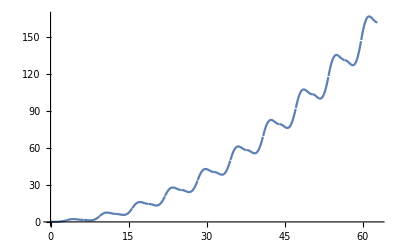

```mathematica
Plot[d33[k],{k,0,20*π}]
```